# Hoja 4: Ecuaciones diferenciales

## Ejercicio1:

Vamos a hallar el valor analítico de la ecuación diferencial:

{{y[x]→1/2 ⅇ^x (-1+Cos[x]^2)}}

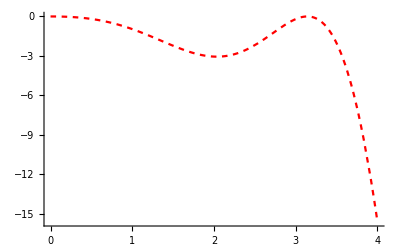

```mathematica
dy=DSolve[{y'[x]==y[x]-Exp[x]*Cos[x]*Sin[x],y[0]==0},y[x],x]
grafica=Plot[Evaluate[y[x]/.dy],{x,0,4},PlotStyle->{Dashing[{0.01,0.01}], RGBColor[1,0,0]},PlotRange-> All]
SetDirectory[NotebookDirectory[]];
```

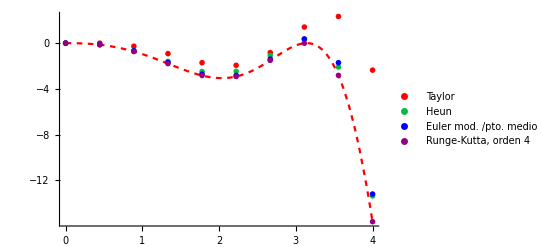

```mathematica
taylor10=Import["taylor010.txt","Table"];
heun10=Import["heun010.txt","Table"];
oilar10=Import["oilar010.txt","Table"];
rk410=Import["rk4010.txt","Table"];
graftaylor10=ListPlot[taylor10,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All,PlotLegends->{"Taylor"}];
grafheun10=ListPlot[heun10,PlotStyle-> {PointSize[0.01],RGBColor[0,0.75,0.25]},PlotRange-> All,PlotLegends->{"Heun"}];
grafoilar10=ListPlot[oilar10,PlotStyle-> {PointSize[0.01],RGBColor[0,0,1]},PlotRange-> All,PlotLegends->{"Euler mod. /pto. medio"}];
grafrk410=ListPlot[rk410,PlotStyle-> {PointSize[0.01],RGBColor[0.59,0,0.5]},PlotRange-> All,PlotLegends->{"Runge-Kutta, orden 4"}];
Show[grafica,graftaylor10,grafheun10,grafoilar10,grafrk410]
```

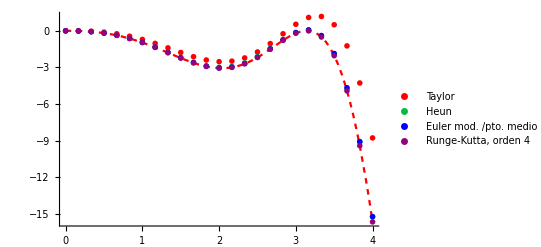

```mathematica
taylor25=Import["taylor025.txt","Table"];
heun25=Import["heun025.txt","Table"];
oilar25=Import["oilar025.txt","Table"];
rk425=Import["rk4025.txt","Table"];
graftaylor25=ListPlot[taylor25,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All,PlotLegends->{"Taylor"}];
grafheun25=ListPlot[heun25,PlotStyle-> {PointSize[0.01],RGBColor[0,0.75,0.25]},PlotRange-> All,PlotLegends->{"Heun"}];
grafoilar25=ListPlot[oilar25,PlotStyle-> {PointSize[0.01],RGBColor[0,0,1]},PlotRange-> All,PlotLegends->{"Euler mod. /pto. medio"}];
grafrk425=ListPlot[rk425,PlotStyle-> {PointSize[0.01],RGBColor[0.59,0,0.5]},PlotRange-> All,PlotLegends->{"Runge-Kutta, orden 4"}];
Show[grafica,graftaylor25,grafheun25,grafoilar25,grafrk425]
```

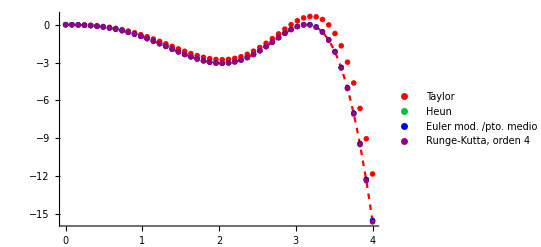

```mathematica
taylor50=Import["taylor050.txt","Table"];
heun50=Import["heun050.txt","Table"];
oilar50=Import["oilar050.txt","Table"];
rk450=Import["rk4050.txt","Table"];
graftaylor50=ListPlot[taylor50,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All,PlotLegends->{"Taylor"}];
grafheun50=ListPlot[heun50,PlotStyle-> {PointSize[0.01],RGBColor[0,0.75,0.25]},PlotRange-> All,PlotLegends->{"Heun"}];
grafoilar50=ListPlot[oilar50,PlotStyle-> {PointSize[0.01],RGBColor[0,0,1]},PlotRange-> All,PlotLegends->{"Euler mod. /pto. medio"}];
grafrk450=ListPlot[rk450,PlotStyle-> {PointSize[0.01],RGBColor[0.59,0,0.5]},PlotRange-> All,PlotLegends->{"Runge-Kutta, orden 4"}];
Show[grafica,graftaylor50,grafheun50,grafoilar50,grafrk450]
```

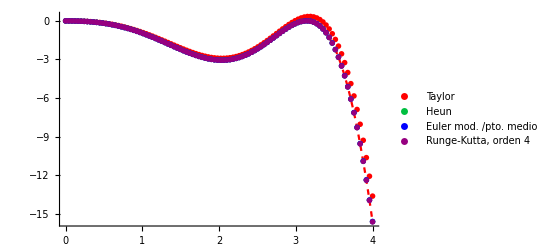

```mathematica
taylor100=Import["taylor100.txt","Table"];
heun100=Import["heun100.txt","Table"];
oilar100=Import["oilar100.txt","Table"];
rk4100=Import["rk4100.txt","Table"];
graftaylor100=ListPlot[taylor100,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All,PlotLegends->{"Taylor"}];
grafheun100=ListPlot[heun100,PlotStyle-> {PointSize[0.01],RGBColor[0,0.75,0.25]},PlotRange-> All,PlotLegends->{"Heun"}];
grafoilar100=ListPlot[oilar100,PlotStyle-> {PointSize[0.01],RGBColor[0,0,1]},PlotRange-> All,PlotLegends->{"Euler mod. /pto. medio"}];
grafrk4100=ListPlot[rk4100,PlotStyle-> {PointSize[0.01],RGBColor[0.59,0,0.5]},PlotRange-> All,PlotLegends->{"Runge-Kutta, orden 4"}];
Show[grafica,graftaylor100,grafheun100,grafoilar100,grafrk4100]
```

## Ejercicio 2 :

Ahora vamos a representar tanto las velocidades como las alturas en función del tiempo para k = 0.004 kg/m en color rojo y para k = 0.01 kg/m en verde.

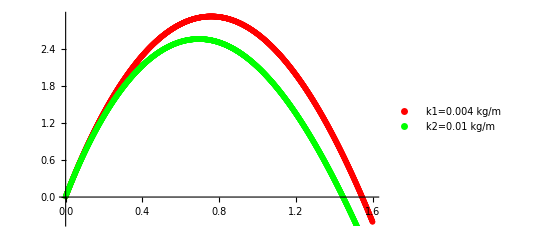

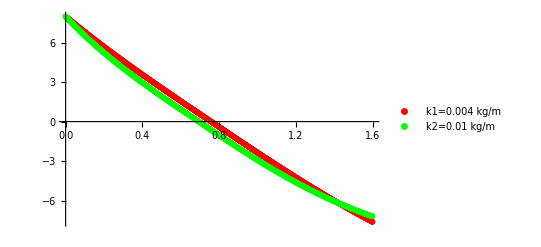

```mathematica
falturak1=Import["alturak1.txt","Table"];
fvelocidadk1=Import["velocidadk1.txt","Table"];
grafalturak1=ListPlot[falturak1,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All, PlotLegends->{"k1=0.004 kg/m"}];
grafvelocidadk1=ListPlot[fvelocidadk1,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All, PlotLegends->{"k1=0.004 kg/m"}];
falturak2=Import["alturak2.txt","Table"];
fvelocidadk2=Import["velocidadk2.txt","Table"];
grafalturak2=ListPlot[falturak2,PlotStyle-> {PointSize[0.01],RGBColor[0,1,0]},PlotRange-> All, PlotLegends->{"k2=0.01 kg/m"}];
grafvelocidadk2=ListPlot[fvelocidadk2,PlotStyle-> {PointSize[0.01],RGBColor[0,1,0]},PlotRange-> All, PlotLegends->{"k2=0.01 kg/m"}];
Show[grafalturak1,grafalturak2]
Show[grafvelocidadk1,grafvelocidadk2]
```